```mathematica
sssol=Block[{s,e,es,p,k1,k2,k3,e0,s0,deqs,ss,cons,seq,
$Assumptions=e0>0&&s0>0&&k1>0&&k2>0&&k3>0},
SetAttributes[{k1,k2,k3,e0,s0},Constant];
ss=-k1 e[t]s[t]+k2 es[t]+k3 es[t]==0;
cons=e[t]+es[t]==e0&&s[t]+es[t]+p[t]==s0;
deqs=dsdt==-k1 e[t]s[t]+k2 es[t]&&dpdt==k3 es[t];
seq=Eliminate[ss&&cons&&deqs,{e[t],es[t],p[t]}]//Simplify;
Solve[seq,{dsdt,dpdt}]/.Rule->Equal
]
```

{{dsdt==-(e0 k1 k3 s[t])/(k2+k3+k1 s[t]),dpdt==(e0 k1 k3 s[t])/(k2+k3+k1 s[t])}}

```mathematica
Block[{vmax,KM,mme},
mme=Eliminate[Union[sssol[[1]],{vmax==e0 k3,KM==(k2+k3)/k1}],{k1,k2,k3}];
Solve[mme,{dsdt,dpdt}]/.{dsdt -> D[s[t],t],dpdt-> D[p[t],t]}
]
```

{{s'[t]→-(vmax s[t])/(KM+s[t]),p'[t]→(vmax s[t])/(KM+s[t])}}

```mathematica
nnsol=Block[{s,e,es,p,k1=100,k2=5,k3=80,e0=0.5,s0=1,tmax=0.15,deqs,inc},
SetAttributes[{k1,k2,k3,e0,s0},Constant];
deqs=D[s[t],t]==-k1 e[t]s[t]+k2 es[t]&&D[e[t],t]==-k1 e[t]s[t]+k2 es[t]+k3 es[t]&&D[es[t],t]==k1 e[t]s[t]-k2 es[t]-k3 es[t]&&D[p[t],t]==k3 es[t];
inc=s[0]==s0&&e[0]==e0&&es[0]==0&&p[0]==0;
NDSolve[deqs&&inc,{s[t],e[t],es[t],p[t]},{t,0,tmax}]
];
```

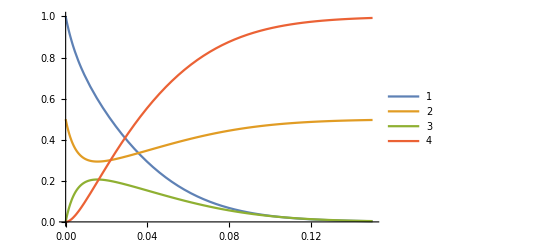

```mathematica
Plot[Evaluate[{s[t],e[t],es[t],p[t]}/.nnsol],{t,0,0.15},PlotLegends->Automatic]
```